Zadatak 1. Napisati program koji za date čvorne tačke računa sve podeljene razlike.

```mathematica
podraz[cv_]:=Module[{m,a},
			m=Length[cv];
			a=Table[0,{i,1,m},{j,1,m}];
			Do[
				a[[i,1]]=cv[[i,2]],
			{i,1,m}];
			Do[
				a⟦i,j⟧=(a⟦i,j-1⟧-a⟦i-1,j-1⟧)/(cv⟦i,1⟧-cv⟦i-(j-1),1⟧),
				{j,2,m},{i,j,m}];
			a]
```

```mathematica
cv={{1,1},{2,3},{4,3},{5,4}}
```

{{1,1},{2,3},{4,3},{5,4}}

```mathematica
podraz[cv]//MatrixForm
```

(1 | 0 | 0 | 0
3 | 2 | 0 | 0
3 | 0 | -2/3 | 0
4 | 1 | 1/3 | 1/4)

Zadatak 2. Napisati program koji za date čvorove kreira Njutnov oblik interpolacionog polinoma. Na izlazu se ispisuje taj polinom.

```mathematica
njutnpol[cv_,x_]:=Module[{c,m,w},
		c=podraz[cv];
		m=Length[cv];
		pol=0;
		w=1;
		Do[
			pol=pol+c[[i,i]]*w;
			w=w*(x-cv[[i,1]]),
		{i,1,m}];
		pol]
```

```mathematica
pol1[x_]=njutnpol[cv,x]
```

1+2 (-1+x)-2/3 (-2+x) (-1+x)+1/4 (-4+x) (-2+x) (-1+x)

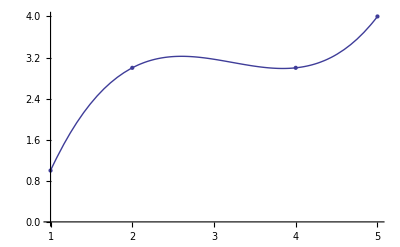

```mathematica
Show[ListPlot[cv],Plot[pol1[x],{x,1,5},PlotRange->All]]
```